```mathematica
IQ[q_,a_,nu_,alpha_,beta_]:=BesselJ[nu,q*a]^2/(q*a)^beta*a^(2*alpha)
```

```mathematica
FullSimplify[FunctionExpand[HypergeometricPFQ[{},{nu+1},-q^2*a^2/4]^2/IQ[q,a,nu,alpha,beta]],Assumptions->a>=0&&q>=0&&S≥0&&n≥0]
```

4^nu a^(-2 alpha) (a q)^(beta-2 nu) Gamma[1+nu]^2

```mathematica
GD[x_,k_,theta_]:=1/theta*(x/theta)^(k-1)*Exp[-x/theta]/Gamma[k]
```

```mathematica
Gamma[-1.2]
```

4.85096

```mathematica
FunctionExpand[Integrate[IQ[q,a,1,2,2]*GD[a,k,theta],{a,0,Infinity},Assumptions->q>0&&k>1&&alpha>1&&beta≥0&&nu>=0&&theta>0&&2 alpha+k>beta]]
```

1/4 k (1+k) (2+k) (3+k) theta^4 HypergeometricPFQ[{3/2,2+k/2,5/2+k/2},{2,3},-4 q^2 theta^2]

```mathematica
IQGD[q_,alpha_,beta_,nu_,k_,theta_]:=1/(√π Gamma[k])q^-beta (1/theta)^k theta^(2 alpha-beta+k) (q theta)^(2 nu) Gamma[1/2+nu] Gamma[2 alpha-beta+k+2 nu] HypergeometricPFQRegularized[{1/2+nu,alpha+1/2 (-beta+k)+nu,alpha+1/2 (1-beta+k)+nu},{1+nu,1+2 nu},-4 q^2 theta^2]
```

```mathematica
FunctionExpand[HypergeometricPFQRegularized[{1/2+nu,alpha+1/2 (-beta+k)+nu,alpha+1/2 (1-beta+k)+nu},{1+nu,1+2 nu},-1/x],Assumptions->x>1]
```

HypergeometricPFQ[{1/2+nu,alpha-beta/2+k/2+nu,1/2+alpha-beta/2+k/2+nu},{1+nu,1+2 nu},-1/x]/(Gamma[1+nu] Gamma[1+2 nu])

```mathematica
Plot[IQGD[q,3,2,1,5,10/5],{q,0.2,.3}]
```

$Aborted

```mathematica
Normal[Series[IQ[q,a,nu,alpha,beta],{q,0,0},Assumptions->a>0&&q>0]]
```

(2^(-2 nu) a^(2 alpha) (a q)^(-beta+2 nu))/Gamma[1+nu]^2

```mathematica
FullSimplify[(4/3*Pi/(2^(- 3/2)/Gamma[1+3/2]))^(1)]
```

2 √2 π^(3/2)

```mathematica
FullSimplify[FunctionExpand[HypergeometricPFQ[{},{nu+1},-q^2*a^2/4]^2/IQ[q,a,nu,alpha,beta]],Assumptions->a>=0&&q>=0&&alpha≥0&&beta≥0&&nu≥0]
```

4^nu a^(-2 alpha) (a q)^(beta-2 nu) Gamma[1+nu]^2

```mathematica
2^(-1+n-0) a^(-6+3 0) q^0 Gamma[1/2 (1+n-0)]^2
```

(2^(-1+n) Gamma[(1+n)/2]^2)/a^6

```mathematica
Normal[Series[IQ[q,a,nu,alpha,beta],{q,0,0},Assumptions->a>0&&q>0]]
```

(2^(-2 nu) a^(2 alpha) (a q)^(-beta+2 nu))/Gamma[1+nu]^2

```mathematica
Normal[Series[(2^(-2 nu) a^(2 alpha) (a q)^(-beta+2 nu))/Gamma[1+nu]^2 HypergeometricPFQ[{},{nu+1},-q^2*a^2/4]^2,{q,0,0},Assumptions->a>0&&q>0]]
```

(2^(-2 nu) a^(2 alpha) (a q)^(-beta+2 nu))/Gamma[1+nu]^2

```mathematica
Solve[s==beta-2*nu&&n==beta+1&&m==2*alpha-n,{beta,nu,alpha}]
```

{{beta→-1+n,nu→1/2 (-1+n-s),alpha→(m+n)/2}}

```mathematica
Solve[s==beta-2*nu&&n==beta+1&&m==2*alpha-n,{m,n,s}]
```

{{m→-1+2 alpha-beta,n→1+beta,s→beta-2 nu}}

```mathematica
FullSimplify[Normal[Series[BesselJ[nu,q*a]^2/(q*a)^(beta)*a^(2*alpha),{q,0,1}]],Assumptions->a>0&&q>0]
```

(4^-nu a^(2 (alpha+nu)) q^(2 nu) (a q)^-beta)/Gamma[1+nu]^2

```mathematica
TeXForm[(4^-nu (a q)^(-beta+2 nu))/Gamma[1+nu]^2]
```

\frac{4^{-\nu } (a q)^{2 \nu -\beta }}{\Gamma (\nu +1)^2}

```mathematica
FullSimplify[Normal[Series[BesselJ[nu,q*a]^2/(q*a)^(beta)*a^alpha,{q,Infinity,0}]],Assumptions->a>0&&q>0]
```

(a^(-3+alpha) (a q)^-beta ((-1+4 nu^2+8 a q) Cos[(nu π)/2-a q]+(-1+4 nu^2-8 a q) Sin[(nu π)/2-a q])^2)/(64 π q^3)

```mathematica
FullSimplify[Expand[(a^(-3+alpha) (a q)^-beta ((-1+4 nu^2+8 a q) Cos[(nu π)/2-a q]+(-1+4 nu^2-8 a q) Sin[(nu π)/2-a q])^2)/(64 π q^3)]/. Cos[(nu π)/2-a q]^2->1/2/.Sin[(nu π)/2-a q]^2->1/2/.Cos[(nu π)/2-a q] Sin[(nu π)/2-a q]->0]
```

(a^(-3+alpha) (a q)^-beta ((1-4 nu^2)^2+64 a^2 q^2))/(64 π q^3)

```mathematica
FullSimplify[(a^(-3+alpha) (a q)^-beta (64 a^2 q^2))/(64 π q^3),Assumptions->q>0 && a>0]
```

(a^alpha (a q)^(-1-beta))/π

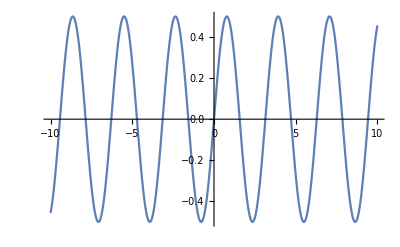

```mathematica
Plot[Sin[x]*Cos[x],{x,-10,10}]
```

```mathematica
4^(-3/2)/Gamma[3/2+1]^2
```

2/(9 π)

```mathematica
Solve[s==gamma+beta-2*nu&&p==gamma+beta+1&&d==alpha+gamma&&s==d-alpha,{alpha,beta,gamma,nu}]
```

{{alpha→d-s,beta→-1+p-s,gamma→s,nu→1/2 (-1+p-s)}}

```mathematica
Solve[s==gamma+beta-2*nu&&p==gamma+beta+1&&d==alpha+gamma&&s==d-alpha,{s,gamma,beta,nu}]
```

{{s→-alpha+d,gamma→-alpha+d,beta→-1+alpha-d+p,nu→1/2 (-1+alpha-d+p)}}